Dynamics

Assumptions used throughout.

```mathematica
$Assumptions=g∈Reals&&zf∈Reals&&x∈Reals&&x0∈Reals&&z0∈Reals&&xd0∈Reals&&zd0∈Reals&&g>0&&zf>0&&x0≠0;
```

Enable assertions.

```mathematica
On[Assert]
```

Configuration vector: CoM position.

```mathematica
q={x[t],z[t]};
```

Dynamics, (3).

```mathematica
dynamics=Thread[D[q,{t,2}]=={0,-g}+q u[t]];
dynamics//MatrixForm
```

(x''[t]==u[t] x[t]
z''[t]==-g+u[t] z[t])

Initial conditions.

```mathematica
initialConditions={x[0]==x0,x'[0]==xd0,z[0]==z0,z'[0]==zd0}
```

{x[0]==x0,x'[0]==xd0,z[0]==z0,z'[0]==zd0}

Conversion to substitution rules.

```mathematica
dynamicsRule=Solve[dynamics,{x''[t],z''[t]}][[1]];
initialConditionsRule=Solve[initialConditions,{x[0],z[0],x'[0],z'[0]}][[1]];
```

Necessary condition for balance

Show that it’s not possible to get past x = 0 if the balistic trajectory doesn’t get you there.

Ballistic trajectory, (6).

```mathematica
ballisticSol=DSolve[{dynamics/.(u[t]->0),initialConditions},{x[t], z[t]},t][[1]];
xbal[t_]=x[t]/.ballisticSol
zbal[t_]=z[t]/.ballisticSol
```

x0+t xd0

1/2 (-g t^2+2 z0+2 t zd0)

Time at which ballistic trajectory intersects z-axis.

```mathematica
T=t/.Solve[xbal[t]==0,t][[1]]
```

-x0/xd0

Z-intercept of ballistic trajectory.

```mathematica
zcrit=zbal[T]
```

1/2 (-(g x0^2)/xd0^2+2 z0-(2 x0 zd0)/xd0)

Time derivative of zcrit along trajectories of the system.

```mathematica
dynamics0={x'[t],z'[t],x''[t],z''[t]}//.Flatten[{dynamicsRule,{t->0},initialConditionsRule}]
zcritdot=FullSimplify[D[zcrit,{{x0,z0,xd0,zd0}}].dynamics0]
```

{xd0,zd0,x0 u[0],-g+z0 u[0]}

(x0 (g x0^2+xd0 (-xd0 z0+x0 zd0)) u[0])/xd0^3

Prove (7).

```mathematica
FullSimplify[Reduce[{zcritdot>0,zcrit≤0,g>0,x0 xd0<0,u[0]≥0},{u0,g,x0,z0,xd0,zd0}]]
```

False

Derive (27).

```mathematica
aBal=Assuming[{g>0,z0>0},Simplify[(xd0/.Solve[zcrit==0/.{zd0->0},xd0][[1]])/x0]]
```

-(√(g/z0))/(√2)

```mathematica
Virtual constraint
```

constraint Virtual

Solve constraint equation for input, (10).

```mathematica
σ=z[t]-f[x[t]];
uSol=u[t]/.Solve[FullSimplify[D[σ,{t,2}]/.dynamicsRule]== 0,u[t]][[1]]
```

(g+x'[t]^2 f''[x[t]])/(z[t]-x[t] f'[x[t]])

Orbital energy controller

Define height trajectory.

```mathematica
Unprotect[Power];
Power[0,0]=1;
Protect[Power];
n = 3;
f[x_]:=Sum[Subscript[c, i] x^i,{i,0,n}];
```

Orbital energy.

```mathematica
h[x_]:=f[x]-D[f[x],x] x;
EoCond[x_]:=(1/2 D[x,t]^2 h[x]^2 + g x^2 f[x] -3 g Integrate[f[x]x,x])
(*EoCond[x_]:=1/2D[x,t]^2h[x]^2- g Integrate[h[x] x,x](*not actually orbital energy, but must also be zero; see eq. (30) in Pratt, Drakunov*)*)
```

Height trajectory constraint equations.

```mathematica
eqs={
f[0]==zf,
f[x[0]]==z[0],
(D[f[x],x]/.x->x[0])==(D[z[t],t]/D[x[t],t]/.t->0),
(EoCond[x[t]]/.t->0)==0};
```

Solve for coefficients.

```mathematica
coefsSol=FullSimplify[Solve[eqs,CoefficientList[f[x],x]]][[1]]
```

{c_0→zf,c_1→(10 x'[0] (z[0] x'[0]-x[0] z'[0])^2+g x[0]^2 (-(9 zf+z[0]) x'[0]+3 x[0] z'[0]))/(2 g x[0]^3 x'[0]),c_2→(2 (g x[0]^2 ((3 zf+2 z[0]) x'[0]-2 x[0] z'[0])-5 x'[0] (z[0] x'[0]-x[0] z'[0])^2))/(g x[0]^4 x'[0]),c_3→(5 (2 x'[0] (z[0] x'[0]-x[0] z'[0])^2+g x[0]^2 (-(zf+z[0]) x'[0]+x[0] z'[0])))/(2 g x[0]^5 x'[0])}

Substitute coefficients into height trajectory.

```mathematica
fSol=FullSimplify[f[x[t]]/.coefsSol]
```

1/(2 g x[0]^5 x'[0])(g x[0]^2 (zf (2 x[0]-5 x[t]) (x[0]-x[t])^2-x[t] (x[0]^2-8 x[0] x[t]+5 x[t]^2) z[0]) x'[0]+10 (x[0]-x[t])^2 x[t] z[0]^2 x'[0]^3+x[0] (x[0]-x[t]) x[t] (g x[0]^2 (3 x[0]-5 x[t])+20 (-x[0]+x[t]) z[0] x'[0]^2) z'[0]+10 x[0]^2 (x[0]-x[t])^2 x[t] x'[0] z'[0]^2)

Sanity checks.

```mathematica
Assert[FullSimplify[((1/2) D[x[t],t]^2 h[x[t]]^2 + g x[t]^2 f[x[t]] -3g (Integrate[f[ξ]ξ,{ξ,0,x[t]}]))/.coefsSol/.t->0]==0]
Assert[Simplify[EoCond[x[t]]/.t->0/.coefsSol]==0]
```

Derive Control law (19).

```mathematica
uCont=FullSimplify[(uSol/.coefsSol)/.{x[0]->x[t],(D[x[t],t]/.t->0)->D[x[t],t],z[0]->z[t],(D[z[t],t]/.t->0)->D[z[t],t]}]
```

(-7 x[t]^2 x'[t]^2+(10 z[t] x'[t]^4)/g-(10 x[t] x'[t]^3 z'[t])/g+(g x[t]^4 x'[t]-3 zf x[t]^2 x'[t]^3)/(z[t] x'[t]-x[t] z'[t]))/x[t]^4

Verify that height trajectory and input trajectory are invariant under scaling of horizontal position and velocity

```mathematica
scaleXandXd={x[0]->k x[0],(D[x[t],t]/.t->0)->k (D[x[t],t]/.t->0),x[t]->k x[t]};
Assert[Assuming[k≠0,Simplify[(fSol/.scaleXandXd)==fSol]]]
Assert[Assuming[k≠0,Simplify[(uTraj/.scaleXandXd)==uTraj]]]
```

Change of variables (21) to arrive at (20).

```mathematica
uContAB=FullSimplify[(uCont/.D[x[t],t]->a[t] x[t]),(D[z[t],t]-a[t]z[t])==b[t]]
```

-7 a[t]^2+(-g a[t]+3 zf a[t]^3)/b[t]-(10 a[t]^3 b[t])/g

Region of attraction

Solve for input trajectory: input as a function of initial state and current horizontal CoM position.

```mathematica
xdSquared=ξ/.Solve[(EoCond[x[t]]/.{D[x[t],t]^2->ξ})==0,ξ][[1]]
uTraj=FullSimplify[(uSol/.{z[t]->f[x[t]],D[x[t],t]^2->xdSquared})/.coefsSol]
```

(10 g c_0 x[t]^2-5 g c_2 x[t]^4-8 g c_3 x[t]^5)/(10 (c_0-c_2 x[t]^2-2 c_3 x[t]^3)^2)

(g^2 x[0]^5 x'[0] (g^2 zf^2 x[0]^10 x'[0]^2-x[t]^3 (-2 x'[0] (z[0] x'[0]-x[0] z'[0])^2+g x[0]^2 ((zf+z[0]) x'[0]-x[0] z'[0])) (5 g zf x[0]^5 x'[0]+5 x[t]^3 (-2 x'[0] (z[0] x'[0]-x[0] z'[0])^2+g x[0]^2 ((zf+z[0]) x'[0]-x[0] z'[0]))+3 x[0] x[t]^2 (5 x'[0] (z[0] x'[0]-x[0] z'[0])^2+g x[0]^2 (-(3 zf+2 z[0]) x'[0]+2 x[0] z'[0])))))/(g zf x[0]^5 x'[0]+5 x[t]^3 (-2 x'[0] (z[0] x'[0]-x[0] z'[0])^2+g x[0]^2 ((zf+z[0]) x'[0]-x[0] z'[0]))+2 x[0] x[t]^2 (5 x'[0] (z[0] x'[0]-x[0] z'[0])^2+g x[0]^2 (-(3 zf+2 z[0]) x'[0]+2 x[0] z'[0])))^3

Change of variables.

```mathematica
uTrajAB=FullSimplify[(uTraj/.{x[0]->1,x'[0]->a[0],x[t]->δ }),(z'[0]-a[0] z[0])==b[0]]
```

(g^2 a[0] (10 (3-2 δ) δ^5 a[0]^2 b[0]^4+g δ^3 a[0] b[0]^2 (zf (10+δ^2 (-33+20 δ)) a[0]+(27-20 δ) δ^2 b[0])-g^2 (zf^2 (-1+5 δ^3-9 δ^5+5 δ^6) a[0]^2-5 zf (-1+δ)^2 δ^3 (1+2 δ) a[0] b[0]+δ^5 (-6+5 δ) b[0]^2)))/((g zf (1+δ^2 (-6+5 δ)) a[0]+g (4-5 δ) δ^2 b[0]-10 (-1+δ) δ^2 a[0] b[0]^2)^3)

Solve using cylindrical decomposition

```mathematica
(*FullSimplify[CylindricalDecomposition[{ForAll[δ,0≤δ≤1,FullSimplify[Numerator[uTrajAB]Denominator[uTrajAB]]≥0&&g>0&&zf>0&&a<0]},{g,zf,b,a}]] *)
pAB=Numerator[uTrajAB];
qAB=Denominator[uTrajAB];
conditions=FullSimplify[CylindricalDecomposition[{ForAll[δ,0≤δ≤1,FullSimplify[pAB qAB]≥0&&g>0&&zf>0&&a[0]<0]},{g,zf,a[0],b[0]}]]
```

a[0]<0&&(7 g)/a[0]+20 b[0]≥√3 √(g (40 zf+(3 g)/a[0]^2))

Same result using Reduce.

```mathematica
conditions=Simplify[Reduce[ForAll[δ,0≤δ≤1,uTrajAB≥0]&&g>=0&&zf>=0&&a[0]<0,b[0],Reals]]
```

a[0]<0&&(7 g)/a[0]+20 b[0]≥√3 √(g (40 zf+(3 g)/a[0]^2))

Manual simplifications, (25).

```mathematica
conditionsManual=a[0]<0&&7g+20b[0] a[0]≤-Sqrt[9g^2+120g zf a[0]^2]
```

a[0]<0&&7 g+20 a[0] b[0]≤-√(9 g^2+120 g zf a[0]^2)

Ensure equivalence.

```mathematica
Assert[FullSimplify[Reduce[Equivalent[conditions,conditionsManual]&&g>0&&zf>0,Reals]]]
```

Additional results

Lowest ratio of CoM position and velocity for which balance can be achieved using (unclipped) orbital energy controller, (26).

```mathematica
amax=FullSimplify[Maximize[{a[0],conditions//.{b[0]-> (zd0-a[0] z0),z0->zf,zd0->0}},{a[0]},Reals],ComplexityFunction->(1000 Count[#,Root[__],All]+LeafCount[#]&)][[1]]
N[amax]
(*amax=Maximize[{a,conditions//.{b-> (zd0-a z0)}},{a},Reals]
Simplify[amax]*)
```

-√(1/10 (5+√15)) √(g/zf)

-0.941965 √(g/zf)

Effect of scaling a

Substitute in definition of b.

```mathematica
conditionsAOnly=FullSimplify[conditions//.{(*a[0]->x'[0]/x[0],*)b[0]-> (z'[0]-a[0] z[0])}]
```

a[0]<0&&(7 g)/a[0]+20 z'[0]≥√3 √(g (40 zf+(3 g)/a[0]^2))+20 a[0] z[0]

```mathematica
conditionsAOnlyScaled=(conditionsAOnly/.{a[0]->c a[0]})&&c>1
```

c a[0]<0&&(7 g)/(c a[0])+20 z'[0]≥√3 √(g (40 zf+(3 g)/(c^2 a[0]^2)))+20 c a[0] z[0]&&c>1

Instance where conditions and scaled conditions aren’t equivalent (but z[0] < 0)

```mathematica
FindInstance[conditionsAOnly&&Not[conditionsAOnlyScaled]&&g>0&&zf==1&&c>1,{a[0],z[0],z'[0],c,g,zf}]
```

{{a[0]→-1,z[0]→-9/16,z'[0]→13/8,c→2,g→1,zf→1}}

Try to find instance where conditions and scaled conditions aren’t equivalent (but z[0] < 0).

```mathematica
FindInstance[(conditionsAOnly/.z'[0]->0)&&Not[(conditionsAOnlyScaled/.z'[0]->0)]&&g>0&&zf>0&&c>1&&z[0]>0,{a[0],z[0],z'[0],c,g,zf}]
```

{}

If z[0] is constrained to be positive and z’[0] = 0, the scaled conditions are equivalent

```mathematica
(*equiv=Assuming[{c>1,z[0]>0},FullSimplify[Reduce[Implies[(conditionsAOnlyScaled/.z'[0]->0),(conditionsAOnlyScaled/.z'[0]->0)]&&g>0&&zf>0,Reals]]]*)
```

If z[0] is constrained to be positive, the scaled conditions are equivalent (requires some time to compute)

```mathematica
(*equiv=FullSimplify[Implies[conditionsOriginal,conditionsAOnlyScaled]&&g>0&&zf>0&&z[0]>0];
equiv=Reduce[equiv];
equiv=FullSimplify[equiv];
Assuming[{c>1,z[0]>0,a<0},Simplify[Reduce[equiv,Reals]]]*)
```

Lowest z0 for which balance can be achieved

```mathematica
zmin=Assuming[a[0]<0,FullSimplify[Minimize[{z[0],conditionsAOnly},{z[0]}]]][[1]]
zminLimit=Limit[zmin,a[0]->-Infinity]
(*Plot[zmin/.{g->gval,zf->zfval,z'[0]->0},{a,-10,0},AxesLabel->{Subscript[a, 0],Subscript[z, min]}]*)
```

(7 g+√3 √(g (3 g+40 zf a[0]^2))+20 a[0] z'[0])/(20 a[0]^2)

0

Maximum value of a_0 for which balance can be achieved at z0 = zf (works, but not pretty)

Alternative variable order

```mathematica
conditionsAlt=FullSimplify[Reduce[ForAll[δ,0≤δ≤1,uTrajAB≥0]&&g>0&&zf>0&&a[0]<0,a,Reals]]
```

b[0]>0&&3 g zf<10 b[0]^2&&2 a[0]≤(g (7 b[0]+√(12 g zf+9 b[0]^2)))/(3 g zf-10 b[0]^2)

Plots

```mathematica
(*SetOptions[Plot,BaseStyle->{FontFamily->"Times",FontSize->12}];*)
gval=9.8;
zfval=1.;
```

```mathematica
xmax=0.8;
xdmax=1.5;
conditionsForPlot=FullSimplify[conditions//.{a[0]->xd0/x0,b[0]-> (zd0-a[0] z0)}]/.{zd0->0,g->gval,zf->zfval};
```

3D slice region plot

```mathematica
plotPoints=50;(*set to 200 for high quality, but takes a long time*)
xGridLines=3;
zGridLines=5;
zmax=2;
xticks=N[Array[#&,3,{-xmax/2,xmax/2}]];
zticks=N[Array[#&,zGridLines,{0,zmax}]];
plt=RegionPlot3D[conditionsForPlot,{x0,-xmax,xmax},{xd0,-xdmax,xdmax},{ z0,0,zmax},PlotPoints->plotPoints,PerformanceGoal->"Quality",AxesLabel->{Style["x_0",FontFamily->"Times",12],Style["(ẋ)_0",FontFamily->"Times",12],Style["z_0",FontFamily->"Times",12]},PlotRangePadding->None,Ticks->{xticks,Automatic,zticks},PlotTheme->"Scientific",MeshFunctions->{#3&},Mesh->zGridLines-2,ViewPoint->{1.8, -1.3, 1.3},FaceGrids->{{-1,0,0},{0,0,-1},{0,1,0}},FaceGridsStyle->Directive[Gray,Dashed]]
(*Export[NotebookDirectory[]<>"../figures/region.pdf",plt];*)
```

-Graphics3D-

2D contours

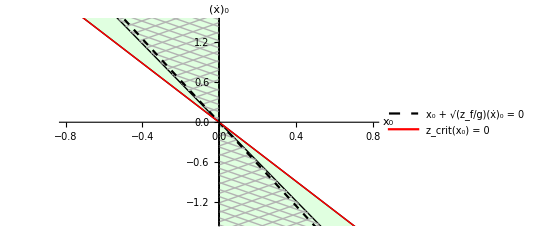

```mathematica
z0val=zfval;
baseColor=LightGreen;(*Lighter[RGBColor[0.368417, 0.506779, 0.709798], 0.3];*)
regionPlot=RegionPlot[conditionsForPlot/.z0->z0val,{x0,-1.1 xmax,1.1 xmax},{xd0,-1.1 xdmax,1.1 xdmax},PlotPoints->60,PerformanceGoal->"Quality",Mesh->30,MeshFunctions->{#1+#2&,#1-#2&},MeshStyle->GrayLevel[0.7],PlotStyle->None,BoundaryStyle->Directive[Thickness[Small], Black](*,PlotLegends->Placed[SwatchLegend[{Style["Orbital energy controller",FontFamily->"Times",12]},LegendMargins->0],{Left,Bottom}]]*)];
swatchRegion=RegionPlot[True,{x,-xmax,xmax},{xd,-xdmax,xdmax},Mesh->2,MeshFunctions->{#1+#2&,#1-#2&},MeshStyle->GrayLevel[0.7],PlotStyle->None,BoundaryStyle->None][[1]];
mixedLegend=SwatchLegend[{LightGreen,White},{"Clipped controller","Orbital energy controller"},LegendMarkers-> {None,Graphics[swatchRegion]}(*,LabelStyle->{FontFamily->"Times",FontSize->12}*)];
axesPlot=Plot[NaN,{x0,-xmax,xmax},AxesLabel->{"x_0","(ẋ)_0"},PlotLegends->Placed[mixedLegend,{Left,Bottom}]];

icpPlot=Plot[{-Sqrt[gval/zfval]x0,(aBal//.{z0->zf,g->gval,zf->zfval}) x0},{x0,-xmax,xmax},PlotStyle->{{Dashed,Black},{Red,Thick}}(*{Black,Dashed,Thin}*),PlotLegends->Placed[{"x_0 + √(z_f/g)(ẋ)_0 = 0", "z_crit(x_0) = 0"},{Right,Top}]];

(*redLine=Plot[(amax/.{g->gval,zf->zfval}) x0,{x0,-xmax,xmax},PlotStyle->{Red,Thickness->Medium}];*)
zcritPlot = RegionPlot[zcrit>0&&xd0/x0<0//.{z0->zf,g->gval,zf->zfval,zd0->0},{x0,-1.1 xmax,1.1 xmax},{xd0,-1.1 xdmax,1.1 xdmax},PlotPoints->60,PlotStyle-> LightGreen,BoundaryStyle->Directive[Thickness[Small], Black](*,PlotLegends->Placed[SwatchLegend[{Style["Clipped controller",FontFamily->"Times",12]}],{Left,Bottom}]*)];
plt=Show[axesPlot,zcritPlot,regionPlot,icpPlot(*,redLine*),PlotRangePadding->None,PlotRange->{{-xmax,xmax},{-xdmax,xdmax}},Frame->None,PlotRangePadding->None]
(*Export[NotebookDirectory[]<>"../figures/regionContourRaw.pdf",plt];*)
```